```mathematica
(* Задача 2 *)
d=1;
T=1;
l=1;
Subscript[l, 1]=0.8;
h=0.1;
τ=h^2/4;
n=Ceiling[l/h];
m=Ceiling[T/τ];
a=1.5;
b=0.25;
u0={0.3,0.2};
f[{S_,B_}]:={1-S-(a S B)/(b+S),((a S)/(b+S) - 1) B}
sol=ConstantArray[{0,0},{m+1,n+1}];
sol⟦1⟧=Table[If[i h < Subscript[l, 1],{0,0},u0],{i,1,n+1}];
```

```mathematica
For[j=1,j≤m,j++,
sol⟦j+1, 1⟧=(1-(2d τ)/h^2)sol⟦j, 1⟧+(2d τ)/h^2 sol⟦j,2⟧+τ f@sol⟦j, 1⟧;
For[i=2,i≤n,i++,
sol⟦j+1, i⟧=(d τ)/h^2(sol⟦j, i+1⟧+sol⟦j, i-1⟧)+(1-(2d τ)/h^2)sol⟦j, i⟧+τ f@sol⟦j, i⟧;
];
sol⟦j+1, n+1⟧=(1-(2d τ)/h^2)sol⟦j, n+1⟧+(2d τ)/h^2 sol⟦j,n⟧+τ f@sol⟦j, n+1⟧;
];
```

```mathematica
Ssol=Table[sol⟦j,i,1⟧,{j,1,m+1},{i,1,n+1}];
Bsol=Table[sol⟦j,i,2⟧,{j,1,m+1},{i,1,n+1}];
xx=Table[k h, {k, 0, n}];
```

```mathematica
Manipulate[
GraphicsGrid[{{
ListLinePlot[Thread[{xx,Ssol⟦j⟧}],PlotStyle->Red,PlotRange->{0,l}, PlotLabel->"S"],
ListLinePlot[Thread[{xx,Bsol⟦j⟧}],PlotStyle->Red,PlotRange->{0,l}, PlotLabel->"B"]
}}]
,{j,1,m +1,1}
]
```

```mathematica
sol⟦1⟧
```

{{0,0},{0,0},{0.3,0.2},{0.3,0.2},{0.3,0.2},{0.3,0.2},{0.3,0.2},{0.3,0.2},{0.3,0.2},{0.3,0.2},{0.3,0.2}}

```mathematica
id[x_]:=x
Thread[1&[{aa,bb,c},{x,y,z},{u,v,t}]]
```

1

{{(-125+3 a^2)/(25+a^2),-(20 a)/(25+a^2)},{(2 a^2 b)/(25+a^2),-(5 a b)/(25+a^2)}}

{(25 a b)/(25+a^2),(-125+3 a^2-5 a b)/(25+a^2)}

(0<a≤5 √(5/3)&&b>0)||(a>5 √(5/3)&&b>(-125+3 a^2)/(5 a))

a>5 √(5/3)&&0<b<(-125+3 a^2)/(5 a)

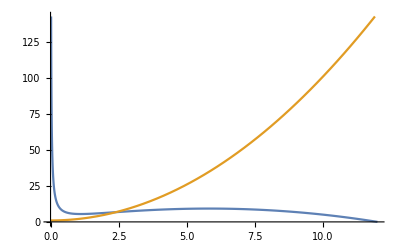

```mathematica
(* Задача 3 *)
Reduce[a-x-(4 x y)/(1+x^2)==0&&b x (1-y/(1+x^2))==0&&a>0&&b>0,{x,y}];
xS=a/5;
yS=Simplify[-(-a+x-a x^2+x^3)/(4x)/.{x->xS}];
equilibriumPoint={xS,yS};
j[{x0_,y0_}]:=Grad[{a-x-(4 x y)/(1+x^2),b x (1-y/(1+x^2))},{x,y}]/.{x->x0,y->y0}
jacobian=Simplify@j@equilibriumPoint
{det, tr}=Simplify@{Det@#,Tr@#}&@jacobian
Reduce[det>0&&tr<0&&a>0&&b>0,{a,b}]
Reduce[det>0&&tr>0&&a>0&&b>0,{a,b}]
Plot[(3 a^2-125)/(5a),{a,0,50},PlotRange->{0,(3 a^2-125)/(5a)/.{a->50}}];
aa=12;
Plot[{((aa-x)(1+x^2))/(4x),1+x^2},{x,0,aa}]
```